## Numerical Simulations of the System

### Set up the system with the same physical parameters

{{x[t]→InterpolatingFunction[{{0.,60.}},<>][t]}}

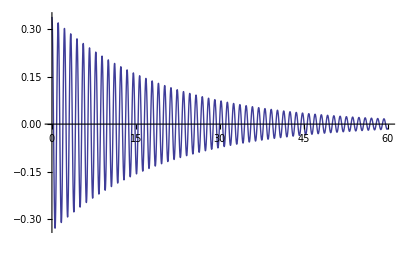

```mathematica
b=.05075;
w0=5.615;
tmax=60;
soln=NDSolve[{x''[t]+2b x'[t] + w0^2 x[t]==0,x[0]==.338,x'[0]==0},{x[t]},{t,0,tmax}]
Plot[Evaluate[x[t]/.soln],{t,0,tmax},PlotRange->All]
```

### Numerical Simulations with varying coupling strength

Set up the general ploting parameters

```mathematica
tmin=60;
tmax=100;
tstep=.05;
time=Table[t,{t,tmin,tmax,tstep}];

amp=.2;
```

#### d=.5

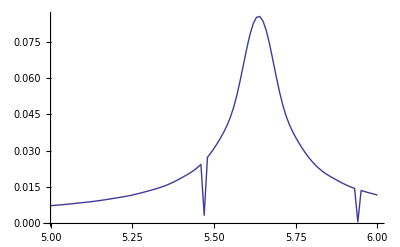

```mathematica
(* The our variable parameter *)
d=.5;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + w0^2 x[t]==d Sin[(amp Sin[w2 t] - x[t])/2],x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

#### d=1

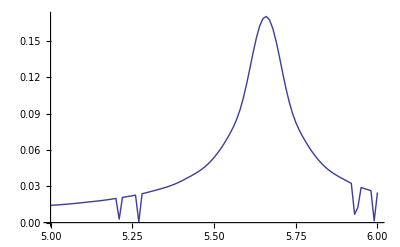

```mathematica
(* The our variable parameter *)
d=1;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + w0^2 x[t]==d Sin[(amp Sin[w2 t] - x[t])/2],x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

#### d=5

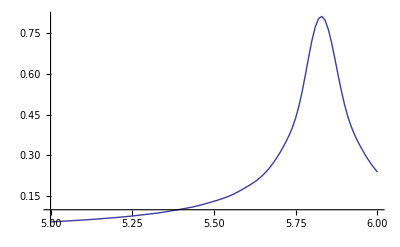

```mathematica
(* The our variable parameter *)
d=5;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + w0^2 x[t]==d Sin[(amp Sin[w2 t] - x[t])/2],x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

### Numerical Simulations with varying coupling strength

Set up the general ploting parameters

```mathematica
tmin=60;
tmax=100;
tstep=.05;
d=2;
```

#### amp = pi/24 = .13

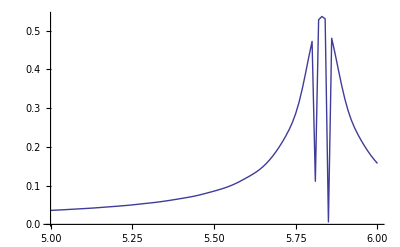

```mathematica
(* The our variable parameter *)
amp=Pi/24;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + w0^2 x[t]==d Sin[(amp Sin[w2 t] - x[t])/2],x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

#### amp = pi/12 = .26

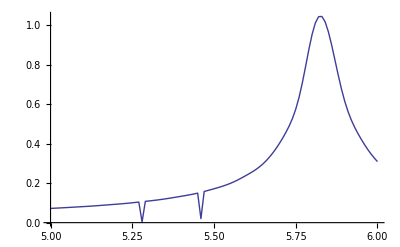

```mathematica
(* The our variable parameter *)
amp=Pi/12;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + w0^2 x[t]==d Sin[(amp Sin[w2 t] - x[t])/2],x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

#### amp = pi/6 = .52

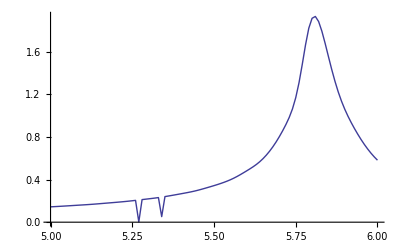

```mathematica
(* The our variable parameter *)
amp=Pi/6;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + w0^2 x[t]==d Sin[(amp Sin[w2 t] - x[t])/2],x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

### Numerical Simulations with Small Angle Approximation - varying d

Set up the general ploting parameters

```mathematica
tmin=60;
tmax=100;
tstep=.05;

amp=.2;
```

#### d=.5

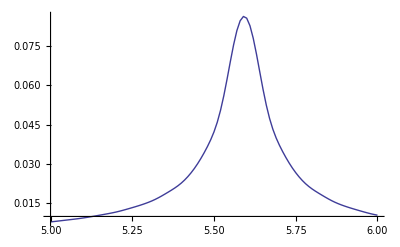

```mathematica
(* The our variable parameter *)
d=.5;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + (w0^2 -d/2)x[t]==d amp Sin[w2 t] /2,x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

#### d=1

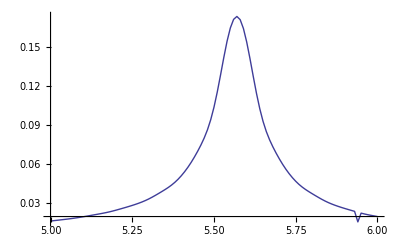

```mathematica
(* The our variable parameter *)
d=1;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + (w0^2 -d/2)x[t]==d amp Sin[w2 t] /2,x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

#### d=5

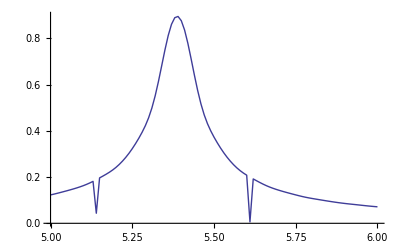

```mathematica
(* The our variable parameter *)
d=5;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + (w0^2 -d/2)x[t]==d amp Sin[w2 t] /2,x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

### Numerical Simulations with Small Angle Approximation - varying amp

Set up the general ploting parameters

```mathematica
tmin=60;
tmax=100;
tstep=.05;

d=2;
```

#### amp=pi/24

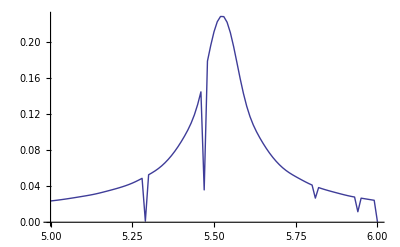

```mathematica
(* The our variable parameter *)
amp=Pi/24;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + (w0^2 -d/2)x[t]==d amp Sin[w2 t] /2,x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

#### amp = pi/12

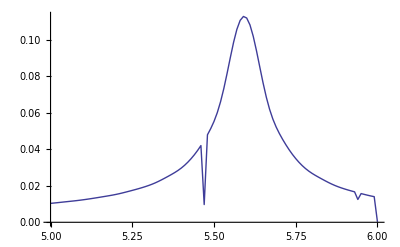

```mathematica
(* The our variable parameter *)
amp = Pi/12;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + (w0^2 -d/2)x[t]==d amp Sin[w2 t] /2,x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
gnd=ListLinePlot[ntdata];

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
gtd = ListLinePlot[fitfinal,PlotStyle->Red];

Show[gnd,gtd];

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```

#### amp = pi/6

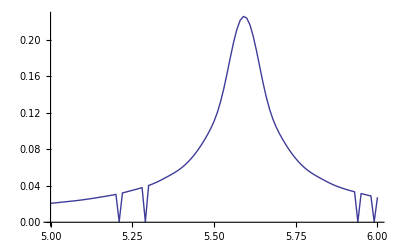

```mathematica
(* The our variable parameter *)
amp=Pi/6;

wvec={};
ampvec={};
Do[
soln=NDSolve[{x''[t]+2b x'[t] + (w0^2 -d/2)x[t]==d amp Sin[w2 t] /2,x[0]==0,x'[0]==0},{x[t]},{t,0,tmax}];
time=Table[t,{t,tmin,tmax,tstep}];
ndata=Flatten[Table[Evaluate[x[t]/.soln],{t,tmin,tmax,tstep}]];ntdata=Transpose[{time,ndata}];
(*gnd=ListLinePlot[ntdata];*)

myfit=a*Sin[w t+phi];
fitparams=FindFit[ntdata,{myfit},{a,w,phi},t,Method->NMinimize];
newfit=myfit/.fitparams;
fitfinal =Transpose[{time,newfit/.t->time}];
(*gtd = ListLinePlot[fitfinal,PlotStyle->Red];*)

(*Show[gnd,gtd];*)

AppendTo[wvec,w2];
AppendTo[ampvec,Abs[a/.fitparams]];
,{w2,5,6,.01}]

ListLinePlot[Transpose[{wvec,ampvec}],PlotRange->All]
```